```mathematica
g1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{2,3},{1},{4},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,2},{1},{3},{5}}]];
```

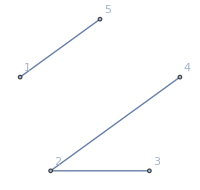

```mathematica
Graph[{1,2,3,4,5},{1<->5,2<->3,2<->4},GraphLayout->"CircularEmbedding", VertexLabels->"Name", ImageSize->200]
```

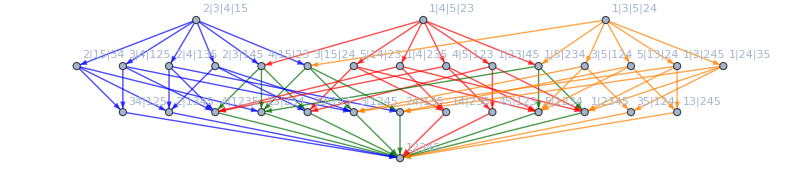

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->800]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,3},{2},{4}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,4},{2},{3}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,3},{1},{2}}]];
```

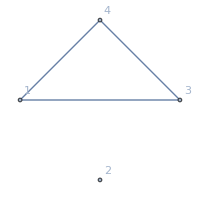

```mathematica
Graph[{1,2,3,4},{1<->3,1<->4,3<->4},GraphLayout->"CircularEmbedding", VertexLabels->"Name", ImageSize->200]
```

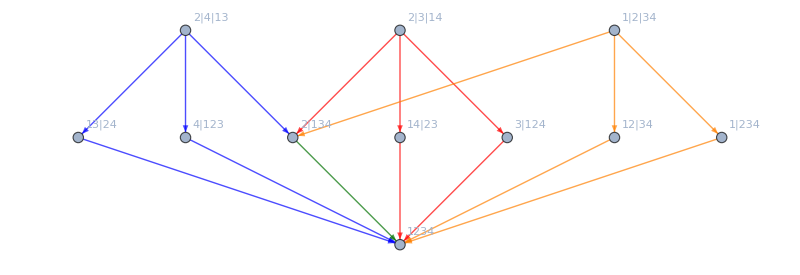

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->800]
```

## A cycle

```mathematica
g1=DeleteDuplicates[Traverse[{{1,2},{3},{4},{5},{6}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,3},{2},{4},{5},{6}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{2,3},{1},{4},{5},{6}}]];
```

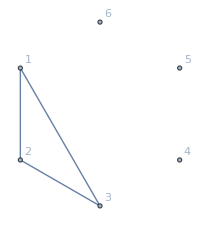

```mathematica
Graph[{1,2,3,4,5,6},{1<->2,2<->3,1<->3},GraphLayout->"CircularEmbedding", VertexLabels->"Name", ImageSize->200]
```

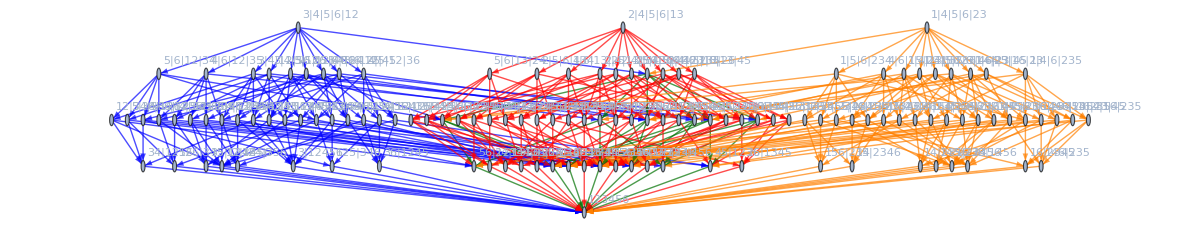

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->1200]
```

```mathematica
x
```

x

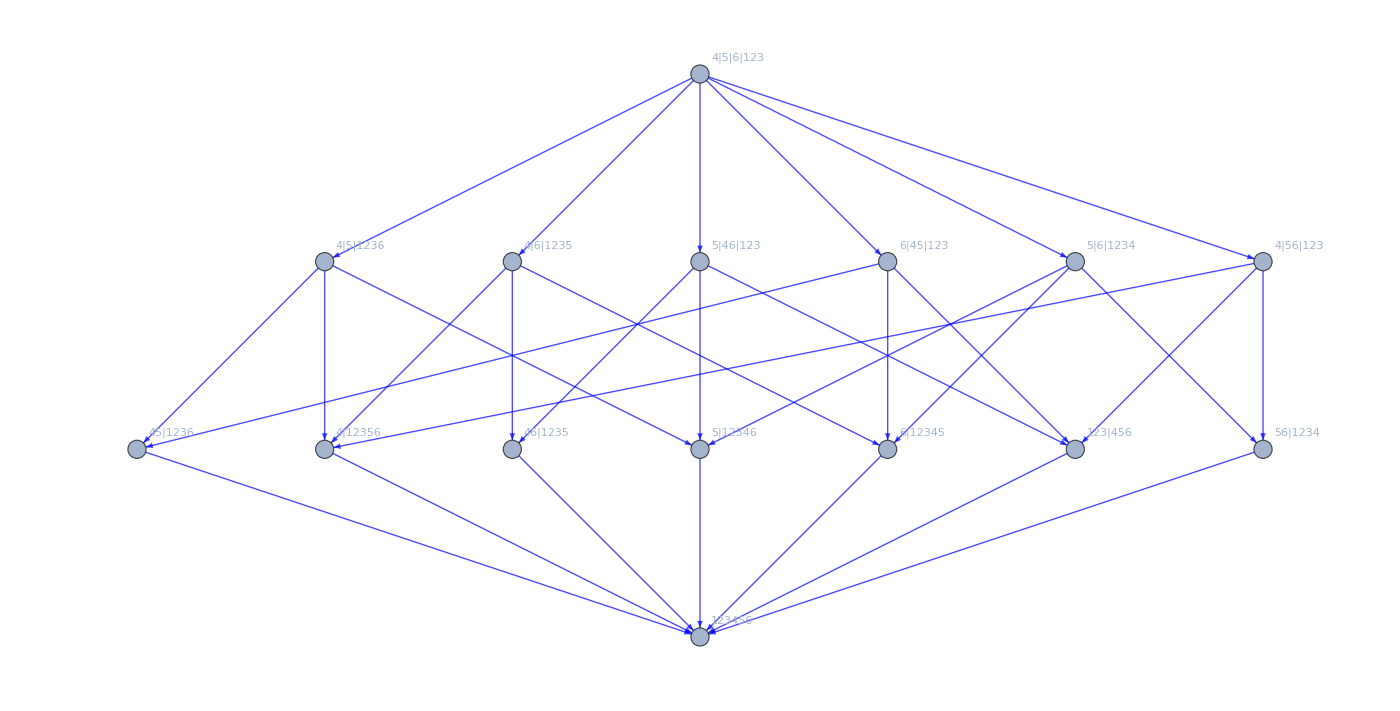

```mathematica
Graph[Sort[DeleteDuplicates[Join[Intersection[g1,g2],Intersection[g1,g3],Intersection[g3,g2]]],SymbolComp2[]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[Intersection[g1,g2],Intersection[g1,g3],Intersection[g3,g2]]]]]],
EdgeStyle->Join[
Map[#->Directive[Blue,Thick]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Red]]&,Select[Intersection[g1,g2],!MemberQ[g3,#]&]],
Map[#->Darker[Yellow]&,Select[Intersection[g3,g2],!MemberQ[g1,#]&]],
Map[#->Darker[Green]&,Select[Intersection[g1,g3],!MemberQ[g2,#]&]]
],
ImageSize->1400]
```

## A quadrilateral

```mathematica
ColorData[1,"ColorList"]
```

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.39598880819409377, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]}

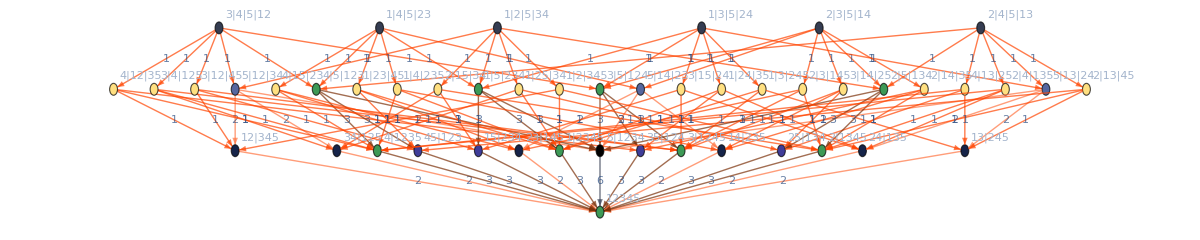

```mathematica
With[
{size=5},
Block[
{graphs=Association[],
sets={{1,2},{2,3},{3,1},{1,4},{4,3},{2,4}},
all, colors,colors2, labels},
Table[
graphs[k]=DeleteDuplicates[Traverse[Join[{sets[[k]]},Map[{#}&,Select[Range[size],!MemberQ[sets[[k]],#]&]]]]],{k,1,Length[sets]}
];
colors2=Map[#[[1]]->Part[Join[ColorData[2,"ColorList"],ColorData[1,"ColorList"],ColorData[3,"ColorList"]],Mod[#[[2]],30]+1]&,Sort[Tally[
Flatten[Map[{#[[1]],#[[2]]}&,Flatten[Values[graphs],2]],1]],#1[[2]]>#2[[2]]&]];
colors=Map[#[[1]]->Part[Join[ColorData[2,"ColorList"],ColorData[1,"ColorList"],ColorData[3,"ColorList"]],Mod[#[[2]],30]+1]&,Sort[Tally[
Flatten[Values[graphs],1]],#1[[2]]>#2[[2]]&]];
labels=Map[#[[1]]->#[[2]]&,Sort[Tally[
Flatten[Values[graphs],1]],#1[[2]]>#2[[2]]&]];

all=DeleteDuplicates[Flatten[Values[graphs],1]];
Graph[all,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->colors, EdgeLabels->labels,
VertexStyle->colors2,
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[all]]], ImageSize->1200]
]
]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,2},{3},{4}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,3},{2},{4}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{2,3},{1},{4}}]];
```

```mathematica
g4=DeleteDuplicates[Traverse[{{1,4},{3},{2}}]];
```

```mathematica
g5=DeleteDuplicates[Traverse[{{2,4},{1},{3}}]];
```

```mathematica
g6=DeleteDuplicates[Traverse[{{3,4},{1},{2}}]];
```

```mathematica
Subsets[{1,2,3,4,5},{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

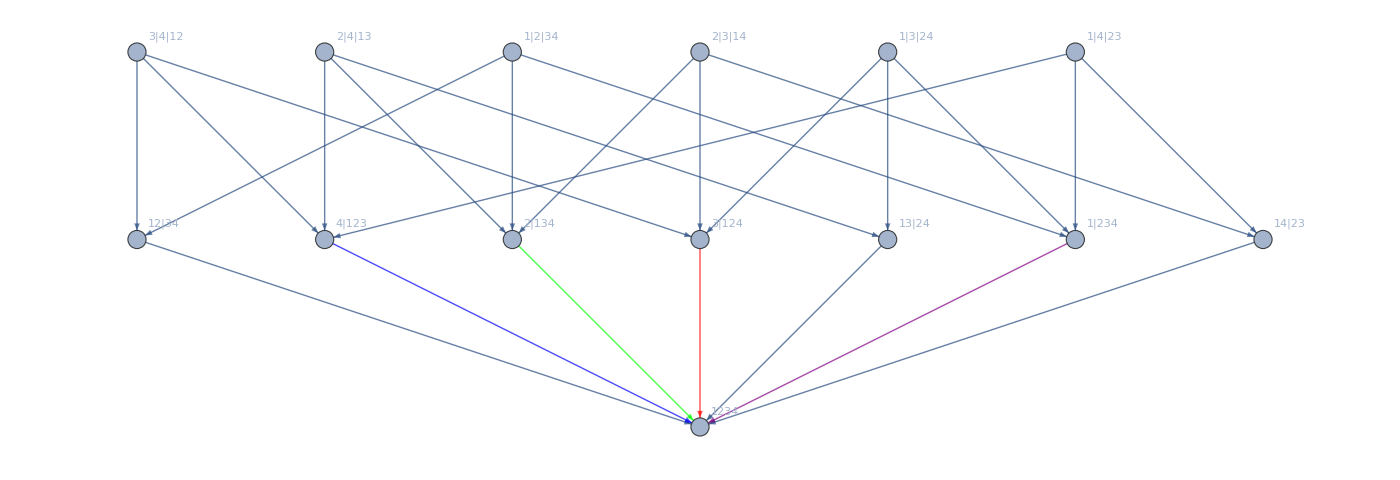

```mathematica
Graph[Sort[DeleteDuplicates[Join[g1,g2,g3,g4,g5,g6]],SymbolComp2[]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3,g4,g5,g6]]]]],
EdgeStyle->Join[
Map[#->Directive[Blue,Thick]&,Intersection[g1,g2,g3]],
Map[#->Directive[Red,Thick]&,Intersection[g4,g5,g1]],
Map[#->Directive[Green,Thick]&,Intersection[g4,g6,g2]],
Map[#->Directive[Purple,Thick]&,Intersection[g3,g6,g5]],
Map[#->Darker[Darker[Red]]&,Select[Intersection[g1,g2],!MemberQ[g3,#]&]],
Map[#->Darker[Yellow]&,Select[Intersection[g3,g2],!MemberQ[g1,#]&]],
Map[#->Darker[Green]&,Select[Intersection[g1,g3],!MemberQ[g2,#]&]]
],
ImageSize->1400]
```

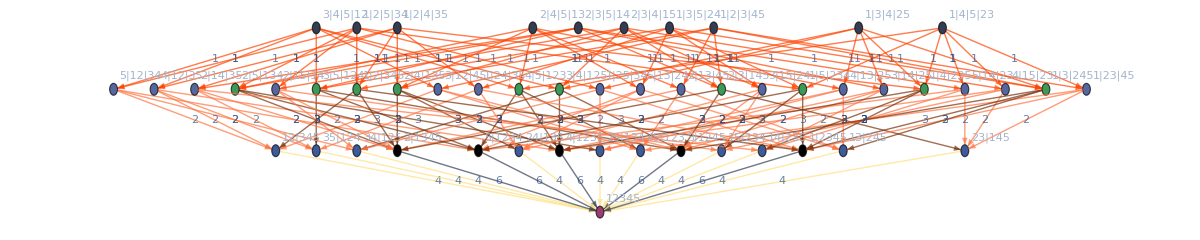

```mathematica
With[
{size=5},
Block[
{graphs=Association[],
sets=Subsets[Range[size],{2}],
all, colors,colors2, labels},
Table[
graphs[k]=DeleteDuplicates[Traverse[Join[{sets[[k]]},Map[{#}&,Select[Range[size],!MemberQ[sets[[k]],#]&]]]]],{k,1,Length[sets]}
];
colors2=Map[#[[1]]->Part[Join[ColorData[2,"ColorList"],ColorData[1,"ColorList"],ColorData[3,"ColorList"]],Mod[#[[2]],30]+1]&,Sort[Tally[
Flatten[Map[{#[[1]],#[[2]]}&,Flatten[Values[graphs],2]],1]],#1[[2]]>#2[[2]]&]];
colors=Map[#[[1]]->Part[Join[ColorData[2,"ColorList"],ColorData[1,"ColorList"],ColorData[3,"ColorList"]],Mod[#[[2]],30]+1]&,Sort[Tally[
Flatten[Values[graphs],1]],#1[[2]]>#2[[2]]&]];
labels=Map[#[[1]]->#[[2]]&,Sort[Tally[
Flatten[Values[graphs],1]],#1[[2]]>#2[[2]]&]];

all=DeleteDuplicates[Flatten[Values[graphs],1]];
Graph[all,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->colors, EdgeLabels->labels,
VertexStyle->colors2,
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[all]]], ImageSize->1200]
]
]
```